# Figure S7. Loss of synchrony between D and V in culture

Data: CSV files beside this notebook, written by dephasing.py of the revision build (period-adaptive and coupling-adaptive models, DD days 0 to 7 without X, forward Euler step 1/64 h, sampled every 0.25 h). Evaluate the notebook (Evaluation > Evaluate Notebook). Each panel and the figure appear below, and Figure_S7.pdf and Figure_S7.png (600 dpi) are written beside the notebook. Solid lines are simulations; dashed lines are least-squares fits of the quadratic decay SI(t) = exp(-D_omega t^2/2) (Myung et al., 2012).

## Style and data

```mathematica
dir = NotebookDirectory[];
font = "Arial"; fsLabel = 8; fsTick = 7; fsLetter = 12;
frameStyle = Directive[Black, AbsoluteThickness[0.5]];
(* hyphens stay hyphens: no operator substitution of "-" in labels; superscripts and subscripts no smaller than 6 pt *)
noSub = PrivateFontOptions -> {"OperatorSubstitution" -> False};
tickStyle = Directive[Black, FontFamily -> font, FontSize -> fsTick, ScriptMinSize -> 6, noSub];
labelStyle = Directive[Black, FontFamily -> font, FontSize -> fsLabel, ScriptMinSize -> 6, noSub];
panelW = 225; panelH = 176; pad = {{48, 8}, {38, 18}};
hex[s_String] := RGBColor @@ (FromDigits[#, 16]/255. & /@ StringPartition[StringDrop[s, 1], 2]);
schedules = {"SP", "LD", "LP", "18:6", "T22", "T23", "T25", "T26"};
col = AssociationThread[schedules -> hex /@ {"#0072B2", "#525252", "#D55E00", "#7B3294", "#009E73", "#56B4E9", "#E69F00", "#CC79A7"}];
readTable[file_String] := Module[{raw = Import[FileNameJoin[{dir, file}], "CSV"]},
   <|"head" -> ToString /@ First[raw], "rows" -> Rest[raw]|>];
column[t_, name_String] := t["rows"][[All, First@FirstPosition[t["head"], name]]];
tA = readTable["S7A_period_adaptive_SI.csv"];
tB = readTable["S7B_coupling_adaptive_SI.csv"];
tC = readTable["S7C_dispersion_period_adaptive.csv"];
tD = readTable["S7D_dispersion_by_schedule.csv"];
tK = readTable["S7_constants.csv"];
constant[name_String] := Pick[column[tK, "value"], column[tK, "quantity"], name][[1]];
perDay = 96; nT = Length[tA["rows"]];
{nT, Dimensions[tC["rows"]], Dimensions[tD["rows"]]}
```

{673,{8,4},{8,7}}

```mathematica
(* outward ticks, open frame, Arial *)
tk[pos_, lab_] := {pos, lab, {0, 0.025}};
dayTicks = Table[tk[perDay d, d], {d, 0, 7}];
letter[l_String] := Text[Style[l, Bold, fsLetter, FontFamily -> font, Black], Scaled[{-0.22, 1.11}], {-1, 1}];
title[s_String] := Text[Style[s, Bold, fsLabel, FontFamily -> font, Black, noSub], Scaled[{0.5, 1.07}], {0, 0}];
txt[s_, c_ : Black] := Style[s, c, fsTick, FontFamily -> font, noSub];
units[pre_] := Row[{"(", pre, Superscript["rad", 2], " ", Superscript["d", "−2"], ")"}];
dOmega = Subscript[Style["D", Italic], Style["ω", Italic]];
common = {Frame -> {{True, False}, {True, False}}, Axes -> False, FrameStyle -> frameStyle,
   FrameTicksStyle -> tickStyle, LabelStyle -> labelStyle, BaseStyle -> labelStyle,
   AspectRatio -> Full, ImageSize -> {panelW, panelH}, ImagePadding -> pad, PlotRangeClipping -> False};
simStyle[s_] := Directive[col[s], AbsoluteThickness[1.1]];
fitStyle[s_] := Directive[col[s], AbsoluteThickness[0.7], AbsoluteDashing[{2.5, 1.8}]];
seriesPlot[data_List, styles_List] := ListLinePlot[data, DataRange -> {0, nT - 1}, PlotStyle -> styles, PlotRange -> All, Sequence @@ common];
lineKey[sty_] := Graphics[{sty, Line[{{0, 0}, {1, 0}}]}, ImageSize -> {14, 6}, PlotRange -> {{0, 1}, {-1, 1}}, AspectRatio -> Full];
mk[g_] := Graphics[g, ImageSize -> {9, 8}, PlotRange -> {{-1, 1}, {-1, 1}}, AspectRatio -> Full];
```

## A. Period-adaptive model

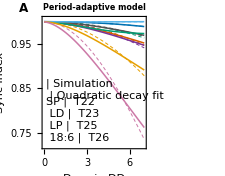

```mathematica
(* key inside the panel: schedules (photoperiods left, T-cycles right), and simulation against the quadratic decay fit *)
keyA = {
   Inset[Grid[Partition[Row[{lineKey[simStyle[#]], " ", txt[#, col[#]]}] & /@ {"SP", "T22", "LD", "T23", "LP", "T25", "18:6", "T26"}, 2],
     Alignment -> Left, Spacings -> {1.0, 0.1}], Scaled[{0.04, 0.04}], {Left, Bottom}],
   Inset[Grid[{{lineKey[Directive[Black, AbsoluteThickness[1.1]]], txt["Simulation"]},
       {lineKey[Directive[Black, AbsoluteThickness[0.7], AbsoluteDashing[{2.5, 1.8}]]], txt["Quadratic decay fit"]}},
     Alignment -> {Left, Center}, Spacings -> {0.4, 0.1}], Scaled[{0.04, 0.36}], {Left, Bottom}]};
pA = Show[
   seriesPlot[Table[column[tA, s <> "_fit"], {s, schedules}], fitStyle /@ schedules],
   seriesPlot[Table[column[tA, s <> "_sim"], {s, schedules}], simStyle /@ schedules],
   PlotRange -> {{0, nT - 1}, {0.72, 1.006}},
   FrameTicks -> {{Table[tk[y, ToString@NumberForm[y, {3, 2}]], {y, {0.75, 0.80, 0.85, 0.90, 0.95, 1.00}}], None}, {dayTicks, None}},
   FrameLabel -> {{"Sync index", None}, {"Days in DD", None}},
   Epilog -> {letter["A"], title["Period-adaptive model"], keyA}]
```

## B. Coupling-adaptive model

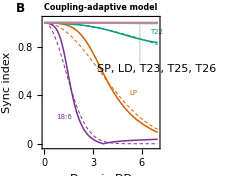

```mathematica
fitB = Pick[column[tD, "schedule"], column[tD, "fit_drawn_coupling"], 1];
fitB = ToString /@ fitB;
labB = {
   Text[txt["18:6", col["18:6"]], {1.2 perDay, 0.22}, {-1, 0}],
   Text[txt["LP", col["LP"]], {5.5 perDay, 0.42}, {-1, 0}],
   Text[txt["T22", col["T22"]], {6.95 perDay, 0.92}, {1, 0}],
   Text[Row[Riffle[txt[#, col[#]] & /@ {"SP", "LD", "T23", "T25", "T26"}, txt[", "]]], {6.95 perDay, 0.62}, {1, 0}],
   {GrayLevel[0.6], AbsoluteThickness[0.4], Line[{{5.9 perDay, 0.665}, {5.9 perDay, 0.985}}]}};
pB = Show[
   seriesPlot[Table[column[tB, s <> "_fit"], {s, fitB}], fitStyle /@ fitB],
   seriesPlot[Table[column[tB, s <> "_sim"], {s, schedules}], simStyle /@ schedules],
   PlotRange -> {{0, nT - 1}, {-0.02, 1.03}},
   FrameTicks -> {{{tk[0, "0"], tk[0.2, "0.2"], tk[0.4, "0.4"], tk[0.6, "0.6"], tk[0.8, "0.8"], tk[1, "1"]}, None}, {dayTicks, None}},
   FrameLabel -> {{"Sync index", None}, {"Days in DD", None}},
   Epilog -> {letter["B"], title["Coupling-adaptive model"], labB}]
```

## C. Fitted dispersion against the frequency mismatch (period-adaptive model)

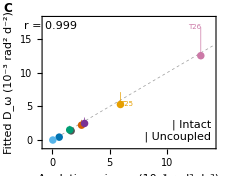

```mathematica
namesC = ToString /@ column[tC, "schedule"];
xC = 1000 column[tC, "analytic_variance"]; yI = 1000 column[tC, "D_intact"]; yU = 1000 column[tC, "D_uncoupled"];
ring[p_, c_, r_ : 2.7] := {{c, AbsolutePointSize[2 r], Point[p]}, {White, AbsolutePointSize[2 r - 2.2], Point[p]}};
square[p_, c_, s_ : 2.6, filled_ : False] := {EdgeForm[{c, AbsoluteThickness[0.9]}], FaceForm[If[filled, c, White]],
    Polygon[{Offset[{-s, -s}, p], Offset[{s, -s}, p], Offset[{s, s}, p], Offset[{-s, s}, p]}]};
dot[p_, c_, r_ : 2.7] := {c, AbsolutePointSize[2 r], Point[p]};
pC = Graphics[{
    {GrayLevel[0.6], AbsoluteThickness[0.5], AbsoluteDashing[{2, 2}], Line[{{0, 0}, {14, 14}}]},
    Table[{col[namesC[[k]]], AbsoluteThickness[0.5], Line[{{xC[[k]], yI[[k]]}, {xC[[k]], yU[[k]]}}]}, {k, Length[namesC]}],
    Table[square[{xC[[k]], yU[[k]]}, col[namesC[[k]]]], {k, Length[namesC]}],
    Table[dot[{xC[[k]], yI[[k]]}, col[namesC[[k]]]], {k, Length[namesC]}],
    Text[txt["T26", col["T26"]], Offset[{-6, 0}, {xC[[8]], yU[[8]]}], {1, 0}],
    Text[txt["T25", col["T25"]], Offset[{6, 0}, {xC[[7]], yI[[7]]}], {-1, 0}],
    Text[Row[{Style["r", Italic], " = ", ToString@NumberForm[constant["pearson_r_intact"], {4, 3}]}, BaseStyle -> {fsTick, FontFamily -> font}],
      Scaled[{0.05, 0.93}], {-1, 0}],
    Inset[Grid[{{mk[dot[{0, 0}, Black]], txt["Intact"]}, {mk[square[{0, 0}, Black]], txt["Uncoupled"]}},
       Alignment -> {Left, Center}, Spacings -> {0.3, 0.2}], Scaled[{0.97, 0.05}], {Right, Bottom}],
    letter["C"]},
   Sequence @@ common,
   PlotRange -> {{-0.6, 14}, {-0.9, 18}},
   FrameTicks -> {{Table[tk[y, y], {y, 0, 15, 5}], None}, {Table[tk[x, x], {x, 0, 10, 5}], None}},
   FrameLabel -> {{Row[{"Fitted ", dOmega, " ", units[Row[{Superscript[10, "−3"], " "}]]}], None},
                  {Row[{"Analytic variance ", units[Row[{Superscript[10, "−3"], " "}]]}], None}}]
```

## D. Dispersion across schedules, with and without D-V coupling

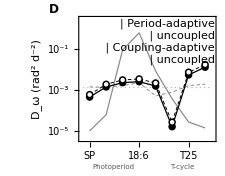

```mathematica
namesD = ToString /@ column[tD, "schedule"];
lg[v_List] := Log10[v];
sD = <|"perI" -> lg@column[tD, "period_intact"], "perU" -> lg@column[tD, "period_uncoupled"],
   "coupI" -> lg@column[tD, "coupling_intact"], "coupU" -> lg@column[tD, "coupling_uncoupled"]|>;
fixedVar = Log10[constant["coupling_adaptive_fixed_variance"]];
gry = GrayLevel[0.55];
solid[c_] := Directive[c, AbsoluteThickness[0.9]];
dashed[c_] := Directive[c, AbsoluteThickness[0.7], AbsoluteDashing[{2.5, 1.8}]];
pts[v_] := Transpose[{Range[Length[v]], v}];
keyD = Inset[Grid[{
     {Graphics[{solid[Black], Line[{{-1, 0}, {1, 0}}], dot[{0, 0}, Black]}, ImageSize -> {22, 7}, PlotRange -> {{-1, 1}, {-1, 1}}, AspectRatio -> Full], txt["Period-adaptive"]},
     {Graphics[{dashed[Black], Line[{{-1, 0}, {1, 0}}], ring[{0, 0}, Black]}, ImageSize -> {22, 7}, PlotRange -> {{-1, 1}, {-1, 1}}, AspectRatio -> Full], txt["uncoupled"]},
     {Graphics[{solid[gry], Line[{{-1, 0}, {1, 0}}], square[{0, 0}, gry, 2.4, True]}, ImageSize -> {22, 7}, PlotRange -> {{-1, 1}, {-1, 1}}, AspectRatio -> Full], txt["Coupling-adaptive"]},
     {Graphics[{dashed[gry], Line[{{-1, 0}, {1, 0}}], square[{0, 0}, gry, 2.4]}, ImageSize -> {22, 7}, PlotRange -> {{-1, 1}, {-1, 1}}, AspectRatio -> Full], txt["uncoupled"]}},
    Alignment -> {Left, Center}, Spacings -> {0.3, 0.05}], Scaled[{0.99, 0.985}], {Right, Top}];
pD = Graphics[{
    {GrayLevel[0.6], AbsoluteThickness[0.5], AbsoluteDashing[{1, 2}], Line[{{0.6, fixedVar}, {8.4, fixedVar}}]},
    {solid[gry], Line[pts[sD["coupI"]]]}, {dashed[gry], Line[pts[sD["coupU"]]]},
    {solid[Black], Line[pts[sD["perI"]]]}, {dashed[Black], Line[pts[sD["perU"]]]},
    square[#, gry, 2.4, True] & /@ pts[sD["coupI"]], square[#, gry, 2.4] & /@ pts[sD["coupU"]],
    dot[#, Black] & /@ pts[sD["perI"]], ring[#, Black] & /@ pts[sD["perU"]],
    Text[txt["Photoperiod", GrayLevel[0.35]], Scaled[{0.25, -0.2}], {0, 0}],
    Text[txt["T-cycle", GrayLevel[0.35]], Scaled[{0.75, -0.2}], {0, 0}],
    keyD, letter["D"]},
   Sequence @@ common,
   PlotRange -> {{0.5, 8.5}, {-5.4, 0.45}},
   FrameTicks -> {{Table[tk[k, Superscript[10, If[k < 0, "−" <> ToString[-k], ToString[k]]]], {k, -5, 0}], None},
                  {Table[tk[i, txt[namesD[[i]], col[namesD[[i]]]]], {i, Length[namesD]}], None}},
   FrameLabel -> {{Row[{dOmega, " ", units[""]}], None}, {None, None}}]
```

## Figure and export

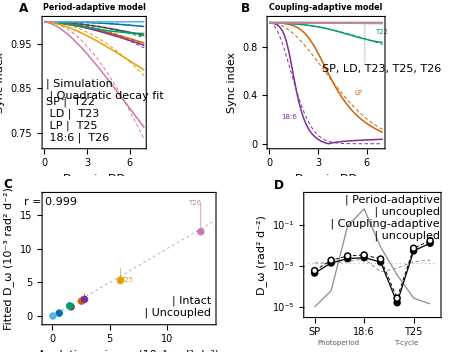

```mathematica
(* one Graphics of 2 x 225 by 2 x 176 printer points (6.25 by 4.89 in, the text width of the SI page);
   Magnification -> 1 keeps the PDF at this size, since PDF export otherwise scales the page by 0.72 *)
wF = 2 panelW; hF = 2 panelH;
fig = Graphics[{
    Inset[pA, {0, hF}, {Left, Top}, {panelW, panelH}], Inset[pB, {panelW, hF}, {Left, Top}, {panelW, panelH}],
    Inset[pC, {0, panelH}, {Left, Top}, {panelW, panelH}], Inset[pD, {panelW, panelH}, {Left, Top}, {panelW, panelH}]},
   PlotRange -> {{0, wF}, {0, hF}}, ImageSize -> {wF, hF}, AspectRatio -> hF/wF, ImagePadding -> None, PlotRangePadding -> None];
Export[FileNameJoin[{dir, "Figure_S7.pdf"}], Style[fig, Magnification -> 1]];
Export[FileNameJoin[{dir, "Figure_S7.png"}], Style[fig, Magnification -> 1], ImageResolution -> 600];
fig
```